```mathematica
h = 6.6261963*10^-35 (*Jerk-sh*)
```

6.6262×10^-35

```mathematica
k=1.6021917*10^-25 (*Jrk/keV*)
```

1.60219×10^-25

```mathematica
c = 299.792458 (*cm/sh*)
```

299.792

```mathematica
B[ν_,T_]:= (2 k^4 ν^3)/(h^3c^2) 1/(Exp[ν/(T)]-1) (*Clark,JCP 70,no.2 1987,p 316*)
```

```mathematica
OpacData = Import["/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AluminumRefinedgroups.csv"]
```

{{0.001,1.×10^10,1.×10^10},{0.001229,1.×10^10,1.×10^10},{0.0015104,1.×10^10,1.×10^10},{0.0018562,1.×10^10,1.×10^10},{0.0022812,1.×10^10,1.×10^10},{0.0028036,1.×10^10,1.×10^10},{0.0034455,1.×10^10,1.×10^10},{0.0042344,1.×10^10,1.×10^10},{0.005204,1.×10^10,1.×10^10},{0.0063956,1.×10^10,1.×10^10},{0.00786,1.×10^10,1.×10^10},{0.0096598,1.×10^10,1.×10^10},{0.011872,1.×10^10,1.×10^10},{0.01459,1.×10^10,1.×10^10},{0.017931,1.×10^10,1.×10^10},{0.022036,8932.1,8932.6},{0.027082,8561.5,8569.},{0.033283,7307.1,7334.8},{0.040904,5610.5,5655.9},{0.05027,3984.1,4031.},{0.06178,2671.3,2710.5},{0.075926,1742.3,1769.8},{0.093311,1174.7,1184.4},{0.11468,778.38,792.36},{0.14093,497.78,506.05},{0.17321,317.6,322.98},{0.21286,202.84,206.18},{0.2616,172.36,209.98},{0.32151,108.33,122.94},{0.39512,75.001,75.79},{0.48559,48.333,49.048},{0.59678,30.697,31.1},{0.73343,19.245,19.467},{0.90136,11.878,11.961},{1.,11.592,11.419},{1.0471,10.413,10.239},{1.0965,9.3274,9.1531},{1.1482,8.3184,8.143},{1.2023,7.4459,7.2684},{1.2589,6.678,6.4995},{1.3183,5.9854,5.806},{1.3804,5.3506,5.1708},{1.4454,4.7667,4.5859},{1.5136,4.4522,4.2836},{1.5849,4.6229,7.4469},{1.6596,8.7125,289.57},{1.7378,4.9355,10.914},{1.8197,4.0839,3.9431},{1.9055,4.9615,4.9201},{1.9953,22.13,46.74},{2.0893,20.163,21.076},{2.1878,22.969,22.814},{2.2909,19.776,19.63},{2.3988,17.658,17.488},{2.5119,16.075,15.903},{2.6303,14.592,14.42},{2.7542,13.105,12.935},{2.884,11.607,11.438},{3.02,10.314,10.14},{3.1623,9.2226,9.0471},{3.3113,8.2327,8.0567},{3.4674,7.2935,7.1181},{3.6308,6.3952,6.2192},{3.8019,5.6533,5.4739},{3.9811,5.0419,4.8614},{4.1687,4.4922,4.3115},{4.3652,3.9725,3.7921},{4.5709,3.477,3.2964},{4.7863,3.0709,2.8884},{5.0119,2.7385,2.5555},{5.2481,2.4411,2.2581},{5.4954,2.1611,1.9785},{5.7544,1.8954,1.7128},{6.0256,1.6794,1.4958},{6.3096,1.5035,1.3199},{6.6069,1.3467,1.1632},{6.9183,1.1994,1.0162},{7.2444,1.06,0.87702},{7.5858,0.94725,0.76408},{7.9433,0.85585,0.67288},{8.3176,0.7745,0.59186},{8.7096,0.69821,0.51597},{9.1201,0.62611,0.44417},{9.5499,0.56803,0.38622},{10.701,0.41258,0.2385},{13.151,0.30609,0.13092},{16.162,0.24517,0.071433},{19.863,0.2094,0.03867},{24.411,0.18752,0.020756}}

```mathematica
tb[Z_,μ_,v_,t_,L_]:=Max[ (μ c t - Z)/(μ c - v),0]
```

```mathematica
tf[Z_,μ_,v_,t_,L_]:=Max[ (L+(μ c t - Z))/(μ c - v),0]
```

```mathematica
s[Z_,μ_,v_,t_,L_]:=Max[c*(tf[Z,μ,v,t,L]-tb[Z,μ,v,t,L]) ,0]
```

```mathematica
logspace[a_,b_,n_]:=Exp[Range[a,b,(b-a)/(n-1)]]
```

```mathematica
nbins=Dimensions[OpacData][[1]]
```

89

```mathematica
groupBounds=Table[If[i≤ nbins,OpacData[[i,1]],30],{i,1,nbins+1}]
groupWidths = Differences[groupBounds];
groupGmid=Table[GeometricMean[groupBounds[[i;;i+1]]],{i,1,nbins}];
```

{0.001,0.001229,0.0015104,0.0018562,0.0022812,0.0028036,0.0034455,0.0042344,0.005204,0.0063956,0.00786,0.0096598,0.011872,0.01459,0.017931,0.022036,0.027082,0.033283,0.040904,0.05027,0.06178,0.075926,0.093311,0.11468,0.14093,0.17321,0.21286,0.2616,0.32151,0.39512,0.48559,0.59678,0.73343,0.90136,1.,1.0471,1.0965,1.1482,1.2023,1.2589,1.3183,1.3804,1.4454,1.5136,1.5849,1.6596,1.7378,1.8197,1.9055,1.9953,2.0893,2.1878,2.2909,2.3988,2.5119,2.6303,2.7542,2.884,3.02,3.1623,3.3113,3.4674,3.6308,3.8019,3.9811,4.1687,4.3652,4.5709,4.7863,5.0119,5.2481,5.4954,5.7544,6.0256,6.3096,6.6069,6.9183,7.2444,7.5858,7.9433,8.3176,8.7096,9.1201,9.5499,10.701,13.151,16.162,19.863,24.411,30}

```mathematica
Tval = 1 (*keV*)
```

1

```mathematica
dens = 1 /10(*g/cc*)
```

1/10

```mathematica
CForm[groupGmid]
```

List(0.001108602724153247,0.0013624542561128429,0.00167439675107186,
   0.0020577568952624115,0.002528946879631915,0.003108022490266118,
   0.0038196367890154163,0.004694232376012079,0.00576911625814561,0.007090092806162696,
   0.008713554269068393,0.010708928312394289,0.013161021236970938,0.016174464133318297,
   0.01987781466861989,0.02442905958075341,0.030022828081311726,0.03689726049451368,
   0.04534582759196264,0.055728633573774264,0.06848874564481379,0.08417084403758822,
   0.10344518103807447,0.1271292743627525,0.15623855254065816,0.19201427186540065,
   0.2359749478228568,0.2900120962994475,0.3564197401940583,0.4380254796241881,
   0.5383218370083086,0.661586241846065,0.8130710084611307,0.9493998104065536,
   1.0232790430767162,1.0715153521998646,1.1220522715096655,1.1749386622287992,
   1.2302745506593233,1.2882576877317673,1.348992705688211,1.4125261625895642,
   1.479106973819,1.5488397722166098,1.6218199776793971,1.6982499462682163,
   1.7782785664793916,1.8621058911887907,1.9498831118813251,2.041759116546318,
   2.137982820323868,2.238756578996475,2.344229280595224,2.4546987024887597,
   2.5704183647803327,2.6915371556045815,2.8183528522880166,2.9512166982449797,
   3.090331050227467,3.23594251957602,3.3884512125748545,3.5481595116341653,
   3.7153651933558294,3.8904683638348736,4.0738202672675685,4.2658187068838265,
   4.466866091568002,4.6773602245283605,4.8978012383109215,5.128640403654754,
   5.370326688386843,5.623409087021858,5.8884388966856065,6.165965111805288,
   6.456539029542066,6.760807368206848,7.079472615950993,7.413134931997393,
   7.7624921990298965,8.128295767256505,8.511343546115384,8.912486912192355,
   9.332526077649074,10.10907908268602,11.862919160139295,14.578973283465471,
   17.917193027927116,22.01989311963162,27.06159640523818)

```mathematica
opacsGmid=Table[Evaluate[σ[groupGmid[[j]],Tval]],{j,1,nbins}];
```

Part::pkspec1: The expression j cannot be used as a part specification.

```mathematica
pcf = Table[{OpacData[[i,3]],ν>groupBounds[[i]]&& ν≤ groupBounds[[i+1]]},{i,1,nbins}];
opacPiece = Piecewise[pcf];
```

```mathematica
opacfunc[νt_]:=opacPiece/.ν->νt
```

```mathematica
opacfunc[groupGmid[[80]]]
```

0.67288

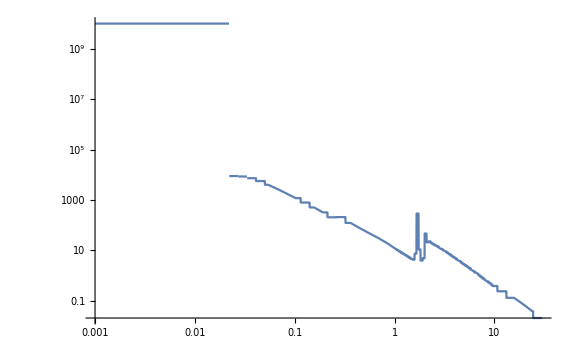

```mathematica
LogLogPlot[{opacfunc[x]+0*B[x,Tval]*200},{x,0.001,30}]
```

```mathematica
Iz[Z_,μ_,ν_,v_,t_,L_,T_,dens_]:= B[γ Dl ν, T]/(γ Dl)^3(1-Exp[-γ Dl (dens*opacfunc[ν*γ*Dl]) s[Z,μ,v,t,L]])/.{Dl-> 1-μ v/c,γ-> 1/Sqrt[(1-β^2)]}/.{β-> v/c}/.{L->L}
```

```mathematica
IzNoMult[Z_,μ_,ν_,v_,t_,L_,T_,dens_]:= B[ν, T]/(γ Dl)^3(1-Exp[-γ Dl (dens*opacfunc[ν]) s[Z,μ,v,t,L]])/.{Dl-> 1-μ v/c,γ-> 1/Sqrt[(1-β^2)]}/.{β-> v/c}/.{L->L}
```

```mathematica
spectrum=Table[{N[groupGmid[[i]]],NIntegrate[Evaluate[Iz[12,μ,T,5.994,1,4/10,Tval,dens]],{μ,0,1},{T,groupBounds[[i]],groupBounds[[i+1]]},PrecisionGoal->5, MaxRecursion->10,Method->"LocalAdaptive"]*2π/c*1/groupWidths[[i]]},{i,1,nbins}]
```

{{0.0011086,1.23142×10^-9},{0.00136245,1.93064×10^-9},{0.0016744,2.91545×10^-9},{0.00205776,4.40164×10^-9},{0.00252895,6.64703×10^-9},{0.00310802,1.00373×10^-8},{0.00381964,1.51553×10^-8},{0.00469423,2.28803×10^-8},{0.00576912,3.45396×10^-8},{0.00709009,5.21332×10^-8},{0.00871355,7.8677×10^-8},{0.0107089,1.18718×10^-7},{0.013161,1.79053×10^-7},{0.0161745,2.70041×10^-7},{0.0198778,4.07119×10^-7},{0.0244291,6.1353×10^-7},{0.0300228,9.24077×10^-7},{0.0368973,1.39088×10^-6},{0.0453458,2.09182×10^-6},{0.0557286,3.14288×10^-6},{0.0684887,4.71634×10^-6},{0.0841708,7.0657×10^-6},{0.103445,0.0000105687},{0.127129,0.0000157713},{0.156239,0.0000234692},{0.192014,0.0000347996},{0.235975,0.0000513721},{0.290012,0.0000754328},{0.35642,0.000109897},{0.438025,0.000157495},{0.538322,0.000218853},{0.661586,0.00028829},{0.813071,0.000353768},{0.9494,0.000373838},{1.02328,0.000400513},{1.07152,0.000409033},{1.12205,0.000412824},{1.17494,0.000414055},{1.23027,0.000413799},{1.28826,0.000412294},{1.34899,0.000409006},{1.41253,0.000403381},{1.47911,0.000395137},{1.54884,0.00039528},{1.62182,0.000534037},{1.69825,0.000990125},{1.77828,0.000870744},{1.86211,0.000513146},{1.94988,0.000511563},{2.04176,0.00107747},{2.13798,0.00115812},{2.23876,0.00114617},{2.34423,0.0011408},{2.4547,0.00111392},{2.57042,0.00108878},{2.69154,0.00105816},{2.81835,0.0010178},{2.95122,0.000964899},{3.09033,0.000906541},{3.23594,0.000846458},{3.38845,0.000783428},{3.54816,0.000715996},{3.71537,0.000644252},{3.89047,0.000574735},{4.07382,0.000510023},{4.26582,0.000448108},{4.46687,0.000387735},{4.67736,0.000329208},{4.8978,0.000276815},{5.12864,0.000231374},{5.37033,0.000191063},{5.62341,0.000154882},{5.88844,0.000122735},{6.16597,0.0000961847},{6.45654,0.0000748334},{6.76081,0.0000573622},{7.07947,0.0000430002},{7.41313,0.0000313829},{7.76249,0.0000226103},{8.1283,0.0000161428},{8.51134,0.0000113194},{8.91249,7.73119×10^-6},{9.33253,5.1181×10^-6},{10.1091,2.64717×10^-6},{11.8629,5.20785×10^-7},{14.579,4.00839×10^-8},{17.9172,1.69851×10^-9},{22.0199,3.54631×10^-11},{27.0616,3.1445×10^-13}}

```mathematica
Export["/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNominal_89.csv",spectrum]
```

/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNominal_89.csv

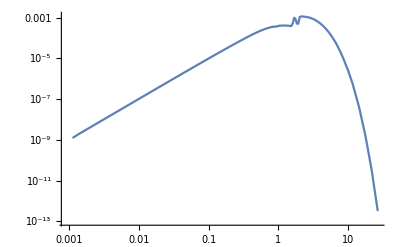

```mathematica
ListLogLogPlot[spectrum,Joined->True]
```

```mathematica
spectrumNoV=Table[{N[groupGmid[[i]]],NIntegrate[Evaluate[IzNoMult[12,μ,T,5.994,1,4/10,Tval,dens]],{μ,0,1},{T,groupBounds[[i]],groupBounds[[i+1]]},PrecisionGoal->5, MaxRecursion->10,Method->"LocalAdaptive"]*2π/c*1/groupWidths[[i]]},{i,1,nbins}]
```

{{0.0011086,1.30504×10^-9},{0.00136245,1.97087×10^-9},{0.0016744,2.97619×10^-9},{0.00205776,4.49336×10^-9},{0.00252895,6.78551×10^-9},{0.00310802,1.02463×10^-8},{0.00381964,1.54709×10^-8},{0.00469423,2.33566×10^-8},{0.00576912,3.52584×10^-8},{0.00709009,5.32179×10^-8},{0.00871355,8.03133×10^-8},{0.0107089,1.21186×10^-7},{0.013161,1.82808×10^-7},{0.0161745,2.75647×10^-7},{0.0198778,4.15563×10^-7},{0.0244291,6.26239×10^-7},{0.0300228,9.43191×10^-7},{0.0368973,1.4196×10^-6},{0.0453458,2.13492×10^-6},{0.0557286,3.20746×10^-6},{0.0684887,4.81293×10^-6},{0.0841708,7.20982×10^-6},{0.103445,0.0000107831},{0.127129,0.0000160892},{0.156239,0.0000239385},{0.192014,0.0000354885},{0.235975,0.0000523763},{0.290012,0.0000768842},{0.35642,0.000111959},{0.438025,0.000160276},{0.538322,0.000222245},{0.661586,0.000291724},{0.813071,0.000356406},{0.9494,0.000370539},{1.02328,0.000403327},{1.07152,0.000408789},{1.12205,0.000412106},{1.17494,0.000412772},{1.23027,0.000412373},{1.28826,0.000410689},{1.34899,0.00040709},{1.41253,0.000401081},{1.47911,0.000392444},{1.54884,0.000394952},{1.62182,0.00057057},{1.69825,0.00114942},{1.77828,0.000750805},{1.86211,0.000443843},{1.94988,0.000527595},{2.04176,0.00126902},{2.13798,0.00110471},{2.23876,0.00115922},{2.34423,0.00113035},{2.4547,0.00110525},{2.57042,0.00108089},{2.69154,0.00104875},{2.81835,0.00100579},{2.95122,0.000950962},{3.09033,0.000892365},{3.23594,0.000832671},{3.38845,0.000769433},{3.54816,0.000701539},{3.71537,0.000629479},{3.89047,0.00056134},{4.07382,0.000498078},{4.26582,0.000436976},{4.46687,0.000377193},{4.67736,0.000319339},{4.8978,0.000268471},{5.12864,0.000224404},{5.37033,0.000185032},{5.62341,0.000149619},{5.88844,0.000118207},{6.16597,0.000092618},{6.45654,0.0000720567},{6.76081,0.0000551385},{7.07947,0.0000412163},{7.41313,0.0000299795},{7.76249,0.0000215903},{8.1283,0.0000154091},{8.51134,0.0000107817},{8.91249,7.33921×10^-6},{9.33253,4.83914×10^-6},{10.1091,2.52168×10^-6},{11.8629,4.82393×10^-7},{14.579,3.60115×10^-8},{17.9172,1.48442×10^-9},{22.0199,2.9916×10^-11},{27.0616,2.53675×10^-13}}

```mathematica
Export["/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNoDopplerNu_89.csv",spectrumNoV]
```

/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNoDopplerNu_89.csv

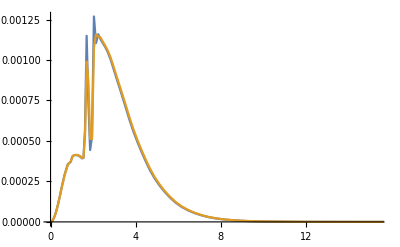

```mathematica
ListPlot[{spectrumNoV,spectrum},Joined->True]
```

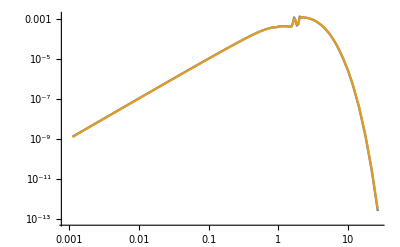

```mathematica
ListLogLogPlot[{spectrumNoV,spectrum},Joined->True]
```

```mathematica
spectrum[[nbins,2]]
```

3.1445×10^-13

```mathematica
Diff = Table[{spectrum[[i,1]],(spectrumNoV[[i,2]]-spectrum[[i,2]])/spectrum[[i,2]]},{i,1,nbins}]
```

{{0.0011086,0.0597835},{0.00136245,0.0208366},{0.0016744,0.0208349},{0.00205776,0.0208365},{0.00252895,0.020833},{0.00310802,0.0208262},{0.00381964,0.0208209},{0.00469423,0.020819},{0.00576912,0.0208133},{0.00709009,0.0208063},{0.00871355,0.0207977},{0.0107089,0.0207871},{0.013161,0.0209712},{0.0161745,0.0207586},{0.0198778,0.0207401},{0.0244291,0.0207146},{0.0300228,0.0206845},{0.0368973,0.0206478},{0.0453458,0.0206026},{0.0557286,0.0205469},{0.0684887,0.0204782},{0.0841708,0.0203969},{0.103445,0.0202908},{0.127129,0.020157},{0.156239,0.0199979},{0.192014,0.0197983},{0.235975,0.0195464},{0.290012,0.0192403},{0.35642,0.0187656},{0.438025,0.0176556},{0.538322,0.0155009},{0.661586,0.011912},{0.813071,0.00745767},{0.9494,-0.00882533},{1.02328,0.00702525},{1.07152,-0.000596046},{1.12205,-0.00173863},{1.17494,-0.00309893},{1.23027,-0.0034459},{1.28826,-0.00389196},{1.34899,-0.00468462},{1.41253,-0.00570171},{1.47911,-0.00681395},{1.54884,-0.000827926},{1.62182,0.0684084},{1.69825,0.160884},{1.77828,-0.137744},{1.86211,-0.135054},{1.94988,0.0313391},{2.04176,0.177774},{2.13798,-0.04612},{2.23876,0.0113879},{2.34423,-0.00915494},{2.4547,-0.00778813},{2.57042,-0.00724512},{2.69154,-0.00889217},{2.81835,-0.0118013},{2.95122,-0.0144443},{3.09033,-0.0156376},{3.23594,-0.0162874},{3.38845,-0.0178635},{3.54816,-0.0201905},{3.71537,-0.0229308},{3.89047,-0.0233071},{4.07382,-0.0234198},{4.26582,-0.0248403},{4.46687,-0.0271872},{4.67736,-0.0299765},{4.8978,-0.0301447},{5.12864,-0.030126},{5.37033,-0.0315623},{5.62341,-0.0339838},{5.88844,-0.0368986},{6.16597,-0.0370817},{6.45654,-0.0371054},{6.76081,-0.0387663},{7.07947,-0.0414844},{7.41313,-0.0447198},{7.76249,-0.0451109},{8.1283,-0.0454519},{8.51134,-0.0475005},{8.91249,-0.0507008},{9.33253,-0.0545034},{10.1091,-0.0474072},{11.8629,-0.0737196},{14.579,-0.101598},{17.9172,-0.126047},{22.0199,-0.156419},{27.0616,-0.193274}}

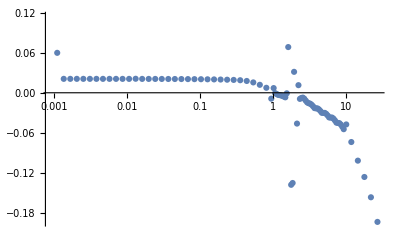

```mathematica
ListLogLinearPlot[Diff]
```

```mathematica
spectrumStationary=Table[{N[groupGmid[[i]]],NIntegrate[Evaluate[Iz[12,μ,T,0*5.994,1,4/10,Tval,dens]],{μ,0,1},{T,groupBounds[[i]],groupBounds[[i+1]]},PrecisionGoal->5, MaxRecursion->10,Method->"LocalAdaptive"]*2π/c*1/groupWidths[[i]]},{i,1,nbins}]
```

{{0.0011086,1.26533×10^-9},{0.00136245,1.9109×10^-9},{0.0016744,2.88564×10^-9},{0.00205776,4.35662×10^-9},{0.00252895,6.57904×10^-9},{0.00310802,9.93456×10^-9},{0.00381964,1.50002×10^-8},{0.00469423,2.2646×10^-8},{0.00576912,3.41857×10^-8},{0.00709009,5.15987×10^-8},{0.00871355,7.78698×10^-8},{0.0107089,1.17499×10^-7},{0.013161,1.77211×10^-7},{0.0161745,2.6726×10^-7},{0.0198778,4.0292×10^-7},{0.0244291,6.07186×10^-7},{0.0300228,9.14495×10^-7},{0.0368973,1.37641×10^-6},{0.0453458,2.06997×10^-6},{0.0557286,3.10988×10^-6},{0.0684887,4.6665×10^-6},{0.0841708,6.99042×10^-6},{0.103445,0.000010455},{0.127129,0.0000155997},{0.156239,0.0000232102},{0.192014,0.0000344088},{0.235975,0.0000507827},{0.290012,0.000074545},{0.35642,0.000108529},{0.438025,0.000155375},{0.538322,0.000215343},{0.661586,0.0002823},{0.813071,0.000343998},{0.9494,0.000355854},{1.02328,0.000387103},{1.07152,0.000391826},{1.12205,0.000394361},{1.17494,0.000394168},{1.23027,0.000392888},{1.28826,0.000390304},{1.34899,0.000385801},{1.41253,0.000378887},{1.47911,0.000369352},{1.54884,0.000370826},{1.62182,0.000543886},{1.69825,0.00111445},{1.77828,0.000720232},{1.86211,0.000415615},{1.94988,0.000497676},{2.04176,0.00122953},{2.13798,0.00106681},{2.23876,0.00112003},{2.34423,0.00109103},{2.4547,0.00106582},{2.57042,0.00104144},{2.69154,0.00100949},{2.81835,0.000966958},{2.95122,0.00091283},{3.09033,0.000855105},{3.23594,0.000796436},{3.38845,0.000734407},{3.54816,0.000667919},{3.71537,0.000597454},{3.89047,0.000531142},{4.07382,0.000469661},{4.26582,0.000410461},{4.46687,0.0003527},{4.67736,0.000296921},{4.8978,0.000248233},{5.12864,0.00020638},{5.37033,0.000169169},{5.62341,0.000135913},{5.88844,0.000106558},{6.16597,0.0000829148},{6.45654,0.0000640897},{6.76081,0.0000487193},{7.07947,0.0000361775},{7.41313,0.0000261255},{7.76249,0.0000186995},{8.1283,0.0000132735},{8.51134,9.23907×10^-6},{8.91249,6.25735×10^-6},{9.33253,4.10458×10^-6},{10.1091,2.1295×10^-6},{11.8629,4.02525×10^-7},{14.579,2.97616×10^-8},{17.9172,1.21984×10^-9},{22.0199,2.45061×10^-11},{27.0616,2.07417×10^-13}}

```mathematica
Export["/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNoV_89.csv",spectrumStationary]
```

/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNoV_89.csv